```mathematica
dir="D:\\newOutput"
```

D:\newOutput

```mathematica
dir=SystemDialogInput["Directory"]
```

D:\grafiliv - stayin alive 2\

```mathematica
GetParent[orgNo_]:=Module[{path,g,n,s,i},
Quiet[
path = StringForm["``\\organisms\\org``.json",dir,orgNo];
{g,n,s,i}=Import[path//ToString];
"parent"/.i
]
]
GetLivingOrganisms[frameNo_]:=Module[{path,file,headings,items,applyHeading,organisms},
path = StringForm["``\\output\\frame``.csv",dir,frameNo];
file=Import[path//ToString];
headings=file//First;
items=file//Rest;
applyHeading[item_]:=MapThread[#1-> #2&,{headings,item}];
items = applyHeading/@items;
organisms="o"/.items//DeleteDuplicates;
Select[organisms,#>=0&]
]
drawRelations[orgs_,steps_]:=Module[{g,gs},
gs=ParallelMap[
NestGraph[
If[#<0,-1,GetParent[#]]&,
#,steps
]&,
orgs
];
g=Parallelize[GraphUnion@@gs];
HighlightGraph[g,orgs,
(*VertexLabels->"Name"*)
GraphLayout->{"LayeredEmbedding","RootVertex"->Min[VertexList[g]]},
VertexLabels->Placed["Name",Tooltip]
]
]
stepsToLCA[a_,b_]:=Module[{lA={a},lB={b}},
While[ContainsNone[lA,lB],
AppendTo[lA,GetParent[Last[lA]]];
AppendTo[lB,GetParent[Last[lB]]];
];
Min[Length[lA],Length[lB]]-1
]
stepsToLCALessThan[a_,b_,max_]:=Monitor[Module[{lA={a},lB={b}},
While[ContainsNone[lA,lB],
If[Length[lA]≤ max &&Length[lB]≤ max ,Return[False]];
AppendTo[lA,GetParent[Last[lA]]];
AppendTo[lB,GetParent[Last[lB]]];
];
True
],lA]
```

```mathematica
step=3009990;
```

```mathematica
living=GetLivingOrganisms[step];
```

```mathematica
RandomChoice[living,2]
```

{333492,334777}

```mathematica
Length[living]
```

1181

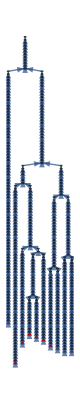

```mathematica
drawRelations[RandomChoice[living,10],100]
```

```mathematica
drawRelations[living,100]
```

$Aborted

```mathematica
stepsToLCALessThan[5,10,100]
stepsToLCA[5,10]
```

False

$Aborted

```mathematica
With[{pair=RandomChoice[living,2]},drawRelations[pair,stepsToLCA@@pair]]
```

$Aborted

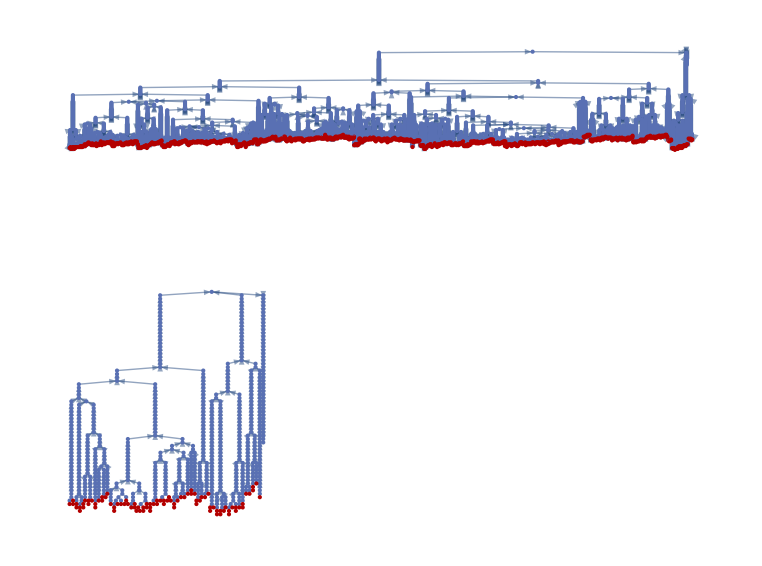

```mathematica
g=drawRelations[living,100]
```

```mathematica
gu=GraphUnion[drawRelations[{334014,334324},200],g];
```

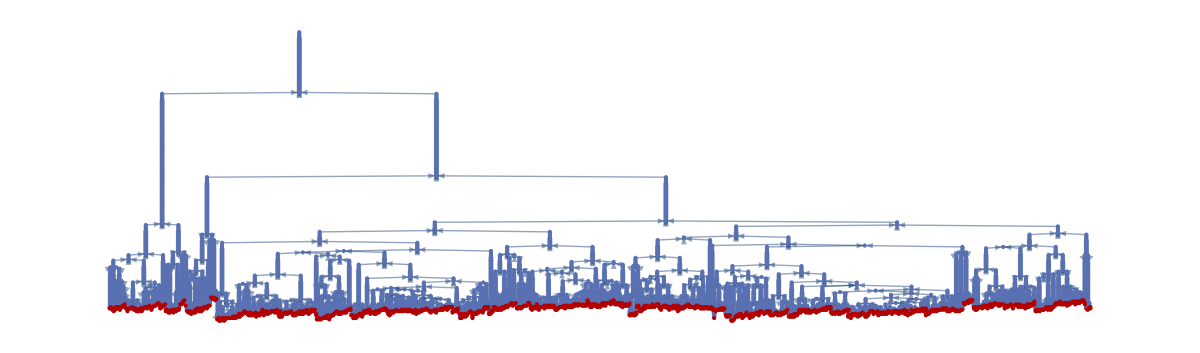

```mathematica
HighlightGraph[
gu,
living,
ImageSize->1200,
VertexLabels->Placed["Name",Tooltip],
GraphLayout->{
"LayeredEmbedding",
"RootVertex"->Min[VertexList[gu]]
}
,EdgeShapeFunction->"Line"
]
```

```mathematica
findSpecies[pool_]:=Module[{orgs = pool,definingSpecimen,s,species={}},
While[Length[orgs]>0,
definingSpecimen=RandomChoice[orgs];
(*orgs=DeleteCases[orgs,definingSpecimen];*)
s=Select[orgs,stepsToLCA[#,definingSpecimen]<7&];
AppendTo[species,s];
orgs=Complement[orgs,s];
PrintTemporary[orgs//Length];
];
species
];
species=findSpecies[living];
```

$Aborted

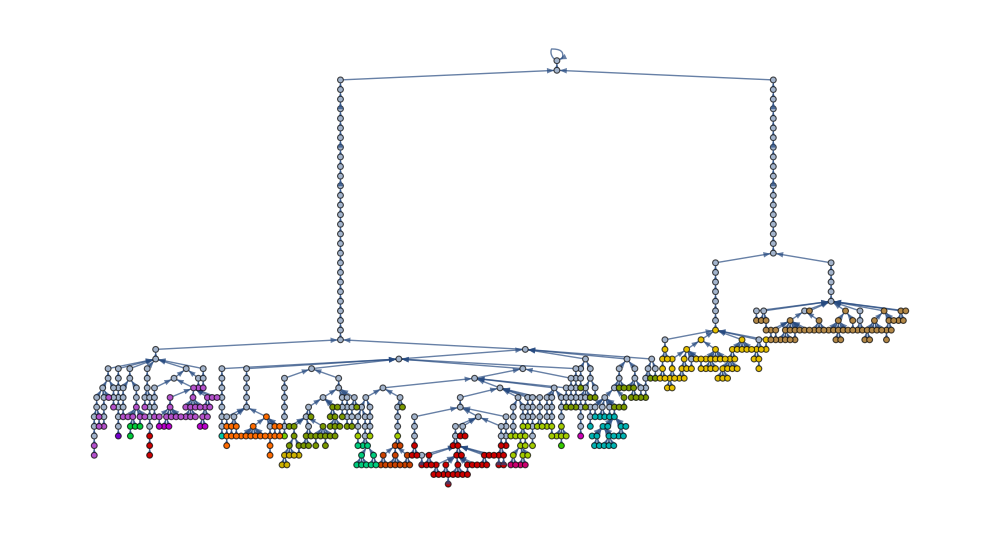

```mathematica
HighlightGraph[
Graph[EdgeList[g],
GraphLayout->{
"LayeredEmbedding",
"RootVertex"->Min[VertexList[g]],
"LeafDistance"->1/2
},
VertexLabels->Placed["Name",Tooltip]],
species,ImageSize->1000]
```